```mathematica
sigmaW = 2
sigmaB = 4
dropoutP = 1
qPrev = 10
normalDistr[z_] = (1/Sqrt[2*Pi])*E^((-z^2)/2)
```

2

4

1

10

(ⅇ^(-z^2/2))/(√(2 π))

```mathematica
phi[x_] = Tanh[x]
qAA[paRsigmaW_, paRsigmaB_, paRdropoutP_, paRqPrev_] = (paRsigmaW/paRdropoutP)* Integrate[phi[(Sqrt[paRqPrev]*z)]^2*normalDistr[z], z] + paRsigmaB^2
```

Tanh[x]

paRsigmaB^2+(paRsigmaW ∫ⅇ^(-z^2/2) Tanh[√paRqPrev z]^2ⅆz)/(paRdropoutP √(2 π))

```mathematica
Plot[qAA[1, 1, 1, x], {x, -1, 1}]
```

1+(∫ⅇ^(-z^2/2) Tanh[√paRqPrev z]^2ⅆz)/(√(2 π))

```mathematica
qAA[1, 1, 1, 1]
```

1+(∫ⅇ^(-z^2/2) Tanh[z]^2ⅆz)/(√(2 π))

```mathematica
Simplify[1+(∫ⅇ^(-z^2/2) Tanh[z]^2 ⅆz)/(√(2 π))]
```

1+(∫ⅇ^(-z^2/2) Tanh[z]^2ⅆz)/(√(2 π))

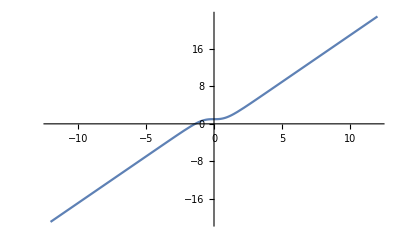

```mathematica
Plot[1+2 (z-Tanh[z]),{z,-12.,12.}]
```